1.

```mathematica
newDisk[{a_,b_}]:=Disk[{(a+b)/2,0},Abs[(b-a)/2]]
```

2.

```mathematica
f[x_]:=Sin[x]
```

3.

```mathematica
replace[{a_,b_}]:=(
					mid=(a+b)/2;
					If[f[mid]>0,{a,N[mid]},{N[mid],b}]
				      )
bisectList=NestList[replace,{4,2},4];
```

4.

```mathematica
graphicBisectList=Table[{Hue[i/5],newDisk[bisectList[[i]]]},{i,1,Length[bisectList]}];
```

5.

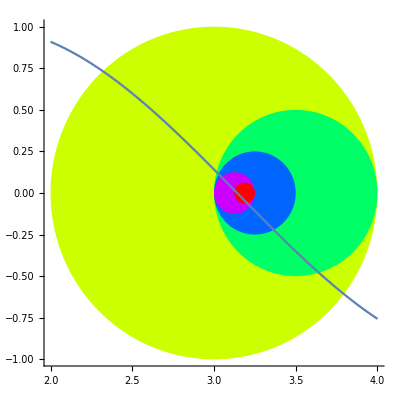

```mathematica
Show[Graphics[graphicBisectList],Plot[Sin[x],{x,4,2}],Axes->True]
```

6.

```mathematica
newton[x_]:=x-f[x]/f'[x]//N
newtonList=NestList[newton,2,4];
```

7.

```mathematica
graphicNewtonList=Table[{Hue[i/5],newDisk[{newtonList[[i]],Pi}]},{i,1,Length[newtonList]}]
```

{{Hue[Rational[1, 5]],Disk[{(2+π)/2,0},1/2 (-2+π)]},{Hue[Rational[2, 5]],Disk[{3.66332,0},0.521724]},{Hue[Rational[3, 5]],Disk[{2.80474,0},0.336849]},{Hue[Rational[4, 5]],Disk[{3.20389,0},0.0622968]},{Hue[1],Disk[{3.14127,0},0.000324371]}}

8.

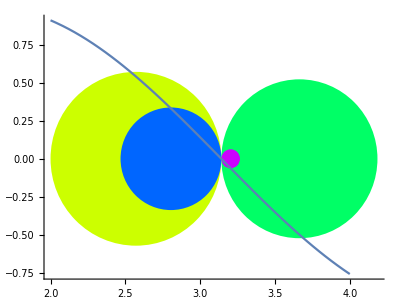

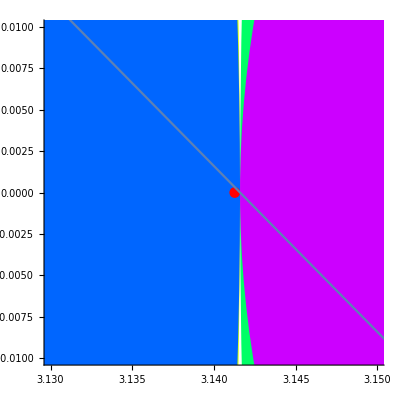

```mathematica
Show[Graphics[graphicNewtonList],Plot[Sin[x],{x,4,2}],Axes->True]
Show[Graphics[graphicNewtonList],Plot[Sin[x],{x,4,2}],Axes->True,PlotRange->{{3.13,3.15},{-.01,.01}}]
```

9.
4 disks are clearly visible.
after zooming in all 5 disks are visible.